```mathematica
(*returns stochastic block model adjacency matrix*)
blockMatrix[n1_,n2_,p_,q_,r_]:=Module[{},m = 
Table[
If[i>=j,0.0,
If[i<=n1&&j<=n1,RandomVariate[BernoulliDistribution[p]],
If[i>n1&&j>n1,RandomVariate[BernoulliDistribution[q]],
RandomVariate[BernoulliDistribution[r]]
]
]
],{i,1,n1+n2},{j,1,n1+n2}];m+Transpose[m]];
blockMatrix2[n1_,n2_,{p_,q_,r_}]:=Module[{},m = 
Table[
If[i>=j,0.0,
If[i<=n1&&j<=n1,RandomVariate[BernoulliDistribution[p]],
If[i>n1&&j>n1,RandomVariate[BernoulliDistribution[q]],
RandomVariate[BernoulliDistribution[r]]
]
]
],{i,1,n1+n2},{j,1,n1+n2}];m+Transpose[m]];
stochBlockMatrix[n1_,n2_,p_,q_,r_]:=Module[{},m = 
Table[
If[i>=j,0,
If[i<=n1&&j<=n1,p,
If[i>n1&&j>n1,q,
r
]
]
],{i,1,n1+n2},{j,1,n1+n2}];m+Transpose[m]];'
densityCalc[mat__]:= 1/Length[mat]/(Length[mat]-1)*Total[mat,2]

(*Function to evolve one element of the matrix, el is the value of the matrix element, a is the element of the squarred matrix *)
evolveStep[el_,a_,ω_,δ_,ϵ_]:= Module[{rand=RandomReal[],ret=0.},If[el==0,If[rand<=δ+ϵ*a,ret=1.,ret=0.],If[rand<=ω,ret=0.,ret=1.]];ret]

(*Function that evolves adjacency matrix mat one time step according to model parameters param (evolvibg block model)*)
(*param= {{n1,n2},{Subscript[ω, p],Subscript[δ, p],Subscript[ϵ, p]},{Subscript[ω, q],Subscript[δ, q],Subscript[ϵ, q]},{Subscript[ω, r],Subscript[δ, r],Subscript[ϵ, r]}} *)
evolve[mat__,param__]:=Module[{ASquarred = mat.mat,new,n1= param[[1,1]],n2=param[[1,2]],ωp=param[[2,1]],δp=param[[2,2]],ϵp=param[[2,3]],ωq=param[[3,1]],δq=param[[3,2]],ϵq=param[[3,3]],ωr=param[[4,1]],δr=param[[4,2]],ϵr=param[[4,3]]},
new=Table[If[i>=j,0,
If[i<=n1&&j<=n1,evolveStep[mat[[i,j]],ASquarred[[i,j]],ωp,δp,ϵp],
If[i>n1&&j>n1,evolveStep[mat[[i,j]],ASquarred[[i,j]],ωq,δq,ϵq],
evolveStep[mat[[i,j]],ASquarred[[i,j]],ωr,δr,ϵr]
]
]
],
{i,1,n1+n2},{j,1,n1+n2}];
new+Transpose[new]]

(*densityEvolution[m__,param__,k_]:=Module[{mat = m,density = Table[0.0,{t,1,k}]},
For[t=1,t<=k,t++,density[[t]]=densityCalc[mat];mat =evolve[mat,param]];density]*)

(* Function that returns the edge density of each school and of the interschool interaactions at each time step from 1 to k*)
densityEvolution[m__,param__,k_]:=Module[{mat=m,density=Table[0.0,{i,1,3},{t,1,k}],n1=param[[1,1]],n2=param[[1,2]]},
For[t=1,t<=k,t++,m1=mat[[1;;n1,1;;n1]];m2=mat[[n1+1;;n1+n2,n1+1;;n1+n2]];m3 = mat[[1;;n1,n1+1;;n1+n2]];
density[[1,t]]=1/n1/(n1-1)Total[m1,2];
density[[2,t]]=1/n2/(n2-1)Total[m2,2];
density[[3,t]]=1/n1/n2 Total[m3,2];
;mat =evolve[mat,param]];
density
];

mfDensityEvolution[p_,q_,r_,param__,k_]:=Module[{mat=blockMatrix[p,q,r,param[[1,1]],param[[1,2]]],density=Table[0.0,{i,1,3},{t,1,k}],n1=param[[1,1]],n2=param[[1,2]]},
For[t=1,t<=k,t++,m1=mat[[1;;n1,1;;n1]];m2=mat[[n1+1;;n1+n2,n1+1;;n1+n2]];m3 = mat[[1;;n1,n1+1;;n1+n2]];
density[[1,t]]=1/n1/(n1-1)Total[m1,2];
density[[2,t]]=1/n2/(n2-1)Total[m2,2];
density[[3,t]]=1/n1/n2/2 Total[m3,2];
;{p,q,r}=probEvolve[p,q,r,param];
density
];
]
(*Function that evolves according to mean field approximation p,q,r by one step wrt to paarameters param*)probEvolve[p0_,q0_,r0_,param__]:=Module[{p=p0,q=q0,r=r0,n1= param[[1,1]],n2=param[[1,2]],ωp=param[[2,1]],δp=param[[2,2]],ϵp=param[[2,3]],ωq=param[[3,1]],δq=param[[3,2]],ϵq=param[[3,3]],ωr=param[[4,1]],δr=param[[4,2]],ϵr=param[[4,3]]},
{(1-ωp)p+(1-p)(δp+ϵp((n1-2)p^2+n2*r^2)),(1-ωq)q+(1-q)(δq+ϵq((n2-2)q^2+n1*r^2)),(1-ωr)r+(1-r)(δr+ϵr((n1-1)p*r+(n2-1)q*r))}]

thDensityEvolution[{p0_,q0_,r0_},param__,k_]:=Module[{p=p0,q=q0,r=r0,n1=param[[1,1]],n2=param[[1,2]],dens = Table[0.0,{j,1,3},{i,1,k}]}, 
For[t=1,t<=k,t++,
dens[[1,t]]=p;
dens[[2,t]]=q;
dens[[3,t]]= r;
{p,q,r}=probEvolve[p,q,r,param]
];dens
]
(* Function that evolves initial matrix m with model parameters param for k time steps. Returns final adjacency matrix*)
run[m0__,param__,k_]:=Module[{m=m0},For[t=1,t<=k,t++,m=evolve[m,param]]; m]

(*Symbolic parameters used throughout notebook where Sym stands for symbolic, S is for Simplified (schools have same parameters), Avg is average i.e. each schol has 
its own parameters but the interaction parameters between them is just the average. In our simplifications, we assume schools have same size to make analysis easier*)
paramSym ={{n1,n2},{Subscript[ω, p],Subscript[δ, p],Subscript[ϵ, p]},{Subscript[ω, q],Subscript[δ, q],Subscript[ϵ, q]},{Subscript[ω, r],Subscript[δ, r],Subscript[ϵ, r]}};
paramSymm={{n1,n2},{ωp,δp,ϵp},{ωq,δq,ϵq},{ωr,δr,ϵr}};
paramSymZ ={{n1,n2},{Subscript[ω, p],0,Subscript[ϵ, p]},{Subscript[ω, q],0,Subscript[ϵ, q]},{Subscript[ω, r],0,Subscript[ϵ, r]}};
paramSymmZ={{n1,n2},{ωp,0,ϵp},{ωq,0,ϵq},{ωr,0,ϵr}};
paramSymmS={{n,n},{ω,δ,ϵ},{ω,δ,ϵ},{ωr,δr,ϵr}};
paramSymmSZ={{n,n},{ω,0,ϵ},{ω,0,ϵ},{ωr,0,ϵr}};
paramSymS={{n,n},{ω,δ,ϵ},{ω,δ,ϵ},{Subscript[ω, r],Subscript[δ, r],Subscript[ϵ, r]}};
paramSymAvg = {{n,n},{Subscript[ω, p],Subscript[δ, p],Subscript[ϵ, p]},{Subscript[ω, q],Subscript[δ, q],Subscript[ϵ, q]},{(Subscript[ω, p]+Subscript[ω, q])/2,(Subscript[δ, p]+Subscript[δ, q])/2,(Subscript[ϵ, p]+Subscript[ϵ, q])/2}};
paramSymmAvg = {{n,n},{ωp,δp,ϵp},{ωq,δq,ϵq},{(ωp+ωq)/2,(δp+δq)/2,(ϵp+ϵq)/2}};
paramSymmAvgZ = {{n,n},{ωp,0,ϵp},{ωq,0,ϵq},{(ωp+ωq)/2,0,(ϵp+ϵq)/2}};

eigenGrad[{p_,q_,r_},{{n1_,n2_},{ωp_,δp_,ϵp_},{ωq_,δq_,ϵq_},{ωr_,δr_,ϵr_}}]:=Eigenvalues[Grad[probEvolve[a,b,c,{{n1,n2},{ωp,δp,ϵp},{ωq,δq,ϵq},{ωr,δr,ϵr}}],{a,b,c}]]/.a->p/.b->q/.c->r;
eigenTest[{p_,q_,r_},{{n1_,n2_},{ωp_,δp_,ϵp_},{ωq_,δq_,ϵq_},{ωr_,δr_,ϵr_}}]:=Eigenvalues[Grad[probEvolve[a,b,c,{{n1,n2},{pωp,pδp,pϵp},{qωq,qδq,qϵq},{rωr,rδr,rϵr}}],{a,b,c}]]/.a->p/.b->q/.c->r/.pωp->ωp/.pδp->δp/.pϵp->ϵp/.qωq->ωq/.qδq->δq/.qϵq->ϵq/.rωr->ωr/.rδr->δr/.rϵr->ϵr;
grad[{p_,q_,r_},{{n1_,n2_},{ωp_,δp_,ϵp_},{ωq_,δq_,ϵq_},{ωr_,δr_,ϵr_}}]:=Grad[probEvolve[a,b,c,{{n1,n2},{ωp,δp,ϵp},{ωq,δq,ϵq},{ωr,δr,ϵr}}],{a,b,c}]/.a->p/.b->q/.c->r;

Options[fastListPlot]={plotPoints->1000,AspectRatio->Full,PlotRange->All,Options[ListLinePlot]}//Flatten;
fastListPlot[data_,opts:OptionsPattern[]]:=Module[{plotData=data,lengths,range=Automatic,points=OptionValue[plotPoints]},While[Depth[plotData]<=2,plotData={plotData}];
lengths=Length/@plotData;
If[NumericQ[points],plotData=Partition[#,Floor[Min[lengths]/points]]&/@plotData;
plotData=Flatten[{Min/@#,Max/@#}ᵀ]&/@plotData;
range={1,Max[lengths]}];
ListLinePlot[plotData,FilterRules[{opts,DataRange->range,Options[fastListPlot]},Options[ListLinePlot]]]]
```

Null'

```mathematica
param={{50,150},{0.01,0.0004,0.0005},{0.01,0.0004,0.0005},{0.05,0.0001,0.001}}
```

{{50,150},{0.01,0.0004,0.0005},{0.01,0.0004,0.0005},{0.05,0.0001,0.001}}

```mathematica
(*param= {{n1,n2},{Subscript[ω, p],Subscript[δ, p],Subscript[ϵ, p]},{Subscript[ω, q],Subscript[δ, q],Subscript[ϵ, q]},{Subscript[ω, r],Subscript[δ, r],Subscript[ϵ, r]}} *)
(* ω:death, δ:birth, ϵ:triadic closure , ω<ϵ(n-2)/4*)
```

```mathematica
Manipulate[Plot[{(1-p) (δ+((-2+n1) p^2+n2 r^2) ϵ)/ω,p},{p,0,1}],{{δ,0.0005},0,0.003,0.000005},{{ ϵ,0.0002},0,0.0003},{{ω,0.003},0.0005,0.01},{{r,0.01},0,1,0.01},{{n1,100},50,200,1},{{n2,100},50,200,1}];
```

```mathematica
Manipulate[With[{R = NSolve[probEvolve[P,χ,ρ,{{n1,n2},{ωp,δp,ϵp},{ωq,δq,ϵq},{ωr,δr,ϵr}}]=={P,χ,ρ},{P,χ,ρ},PositiveReals][[All,3,2]]},Manipulate[With[{pIntersection = NSolve[{(1-p) (δp+((-2+n1) p^2+n2 r^2) ϵp)/ωp==p,p>0},p,Reals][[All,1,2]],qIntersection = NSolve[{(1-q) (δq+((-2+n2) q^2+n1 r^2) ϵq)/ωq==q,q>0},q,Reals][[All,1,2]]},{Show[Plot[{(1-p) (δp+((-2+n1) p^2+n2 r^2) ϵp)/ωp,p},{p,0,1},Frame->True,PlotRange->{{0,1},Automatic},PlotLabel->"(1 - p)/ω_p (δ_p+((n_1-2) p^2+n_2 (r^*)^2) ϵ_p)"],ListPlot[Table[Callout[{pIntersection[[i]],pIntersection[[i]]},+"p^* = "<> ToString[NumberForm[pIntersection[[i]],{5,5}]]],{i,1,Length[pIntersection]}]]],Show[Plot[{(1-q) (δq+((-2+n2) q^2+n1 r^2) ϵq)/ωq,q},{q,0,1},Frame->True,PlotRange->{{0,1},Automatic},PlotLabel->"(1 - q)/ω_q (δ_q+((n_2-2) q^2+n_1 (r^*)^2) ϵ_q)"],ListPlot[Table[Callout[{qIntersection[[i]],qIntersection[[i]]},+"q^* = "<> ToString[NumberForm[qIntersection[[i]],{5,5}]]],{i,1,Length[qIntersection]}]]]}],{{r,R[[1]],"r^*"},R,ControlType->Setter}]],{{δp,0.00015,"δ_p"},0,0.003,0.000005},{{ ϵp,0.0001515,"ϵ_p"},0,0.0003},{{ωp,0.003,"ω_p"},0.0005,0.01},{{δq,0.0001,"δ_q"},0,0.003,0.000005},{{ ϵq,0.000127,"ϵ_q"},0,0.0003},{{ωq,0.003,"ω_q"},0.0005,0.01},{{δr,0.00039,"δ_r"},0,0.003,0.000005},{{ ϵr,6.5*10^(-6),"ϵ_r"},0,0.0003},{{ωr,0.00301,"ω_r"},0.0005,0.01},{{n1,73,"n_1"},50,200,1},{{n2,68,"n_2"},50,200,1}];
```

```mathematica
param={{73,68},{0.003,0.00015,0.0001515},{0.003,0.0001,0.000127},{0.00301,0.00039,6.5*10^(-6)}};
m = blockMatrix[param[[1,1]],param[[1,2]],0.5,0.5,0.1];
```

```mathematica
densit = densityEvolution[m,param,10000];
```

```mathematica
thDensit=thDensityEvolution[0.3,0.5,0.1,param,10000];
```

```mathematica
ListPlot[densit~Join~thDensit,PlotLabels->{p,q,r}]
```

-Graphics-

```mathematica
mm = blockMatrix[param[[1,1]],param[[1,2]],0.329,0.5,0.1];
densitt = densityEvolution[mm,param,3000];
```

```mathematica
thDensitt[[All,3000]]
```

{0.301138,0.0999621,0.120614}

```mathematica
thDensitt=thDensityEvolution[0.329,0.5,0.1,param,3000];
ListPlot[densitt~Join~thDensitt,PlotLabels->{p,q,r}]
```

-Graphics-

```mathematica
Manipulate[paramOut ={{n1,n2},{ωp,δp,ϵp},{ωq,δq,ϵq},{ωr,δr,ϵr}};lastSol =NSolve[{(1-p) (δp+((-2+n1) p^2+n2 r^2) ϵp)+p (1-ωp),(1-q) (δq+((-2+n2) q^2+n1 r^2) ϵq)+q (1-ωq),(1-r) (δr+((-1+n1) p r+(-1+n2) q r) ϵr)+r (1-ωr)}=={p,q,r},{p,q,r},PositiveReals][[All,All,2]] ;
With[{s=NSolve[{(1-p) (δp+((-2+n1) p^2+n2 r^2) ϵp)+p (1-ωp),(1-q) (δq+((-2+n2) q^2+n1 r^2) ϵq)+q (1-ωq),(1-r) (δr+((-1+n1) p r+(-1+n2) q r) ϵr)+r (1-ωr)}=={p,q,r},{p,q,r},PositiveReals],par = {{n1,n2},{ωp,δp,ϵp},{ωq,δq,ϵq},{ωr,δr,ϵr}}},Table[ToString[s[[i]]]<>", Eigenvalues: "<> ToString[eigenGrad[s[[i]][[All,2]],par]],{i,1,Length[s]}]],{{δp,0.00015,"δ_p"},0,0.003,0.000005,Appearance->"Labeled"},{{ ϵp,0.0001515,"ϵ_p"},0,0.0006,Appearance->"Labeled"},{{ωp,0.003,"ω_p"},0.0005,0.02,Appearance->"Labeled"},{{δq,0.00015,"δ_q"},0,0.006,0.00005,Appearance->"Labeled"},{{ ϵq,0.0001515,"ϵ_q"},0.000145,0.000160,0.000001,Appearance->"Labeled"},{{ωq,0.003,"ω_q"},0.0005,0.02,Appearance->"Labeled"},{{δr,0.00039,"δ_r"},0,0.006,0.000005,Appearance->"Labeled"},{{ ϵr,6.5*10^(-6),"ϵ_r"},0,0.0006,Appearance->"Labeled"},{{ωr,0.00301,"ω_r"},0.0005,0.02,Appearance->"Labeled"},{{n1,73,"n_1"},50,200,1,Appearance->"Labeled"},{{n2,73,"n_2"},50,200,1,Appearance->"Labeled"},SaveDefinitions->True]
```

```mathematica
multRuns = Table[densityEvolution[blockMatrix[paramOut[[1,1]],paramOut[[1,2]],lastSol[[i,1]],lastSol[[i,2]],lastSol[[i,3]]],paramOut,10000],{i,1,Length[lastSol]}];
```

```mathematica
Manipulate[ListPlot[multRuns[[i]],PlotLabels->{p,q,r},MaxPlotPoints->1000],{i,1,Length[lastSol],1,Appearance->"Labeled"}]
```

Part::partd: Part specification multRuns⟦2⟧ is longer than depth of object.

Part::pkspec1: The expression Charting`ChartLabelingDump`getLength[2] cannot be used as a part specification.

Part::pkspec1: The expression False cannot be used as a part specification.

ListPlot::lpn: multRuns⟦2⟧ is not a list of numbers or pairs of numbers.

Part::partd: Part specification multRuns⟦2⟧ is longer than depth of object.

Part::pkspec1: The expression Charting`ChartLabelingDump`getLength[2] cannot be used as a part specification.

Part::pkspec1: The expression False cannot be used as a part specification.

ListPlot::lpn: multRuns⟦2⟧ is not a list of numbers or pairs of numbers.

Part::partd: Part specification multRuns⟦2⟧ is longer than depth of object.

Part::pkspec1: The expression Charting`ChartLabelingDump`getLength[2] cannot be used as a part specification.

Part::pkspec1: The expression False cannot be used as a part specification.

ListPlot::lpn: multRuns⟦2⟧ is not a list of numbers or pairs of numbers.

Part::partd: Part specification multRuns⟦2⟧ is longer than depth of object.

Part::pkspec1: The expression Charting`ChartLabelingDump`getLength[2] cannot be used as a part specification.

Part::pkspec1: The expression False cannot be used as a part specification.

ListPlot::lpn: multRuns⟦2⟧ is not a list of numbers or pairs of numbers.

Part::partd: Part specification multRuns⟦2⟧ is longer than depth of object.

Part::pkspec1: The expression Charting`ChartLabelingDump`getLength[2] cannot be used as a part specification.

Part::pkspec1: The expression False cannot be used as a part specification.

ListPlot::lpn: multRuns⟦2⟧ is not a list of numbers or pairs of numbers.

Part::partd: Part specification multRuns⟦2⟧ is longer than depth of object.

Part::pkspec1: The expression Charting`ChartLabelingDump`getLength[2] cannot be used as a part specification.

Part::pkspec1: The expression False cannot be used as a part specification.

ListPlot::lpn: multRuns⟦2⟧ is not a list of numbers or pairs of numbers.

```mathematica
thMultRuns = Table[thDensityEvolution[lastSol[[i]],paramOut,100000],{i,1,Length[lastSol]}];
```

```mathematica
Manipulate[fastListPlot[thMultRuns[[i]],PlotLabels->{p,q,r}],{i,1,Length[thMultRuns],1,Appearance->"Labeled"}]
```

```mathematica
fastListPlot[thDensityEvolution[lastSol[[3]],paramOut,200000],PlotLabels->{p,q,r}]
```

-Graphics-

```mathematica
m = blockMatrix[paramOut[[1,1]],paramOut[[1,2]],0.331063,0.5, 0.3];
```

```mathematica
density = densityEvolution[m,paramOut,1500];
```

```mathematica
ListPlot[density,PlotLabels->{p,q,r}]
```

-Graphics-

```mathematica
m = blockMatrix[paramOut[[1,1]],paramOut[[1,2]],0.5,0.5, 0.3];
```

```mathematica
density = densityEvolution[m,paramOut,1500];
thDensity=thDensityEvolution[0.5,0.5, 0.3,paramOut,1500];
```

```mathematica
ListPlot[density~Join~thDensity,PlotLabels->{p,q,r}]
```

-Graphics-

```mathematica
m = blockMatrix[paramOut[[1,1]],paramOut[[1,2]],0.331063, 0.6, 0.3];
density = densityEvolution[m,paramOut,40000];
thDensity=thDensityEvolution[0.331063, 0.6, 0.3,paramOut,40000];
ListPlot[density~Join~thDensity,PlotLabels->{p,q,r,pth,qth,rth}]
```

-Graphics-

-Graphics-

```mathematica
thDensity=thDensityEvolution[0.333, 0.279993, 0.149002,paramOut,40000];
ListPlot[thDensity,PlotLabels->{p,q,r}]
```

-Graphics-

```mathematica
thDensity=thDensityEvolution[0.641205, 0.356188, 0.320628,paramOut,40000];
ListPlot[thDensity,PlotLabels->{p,q,r}]
```

-Graphics-

```mathematica
thDensity=thDensityEvolution[0.102815,  0.265238, 0.0913911,paramOut,40000];
ListPlot[thDensity,PlotLabels->{p,q,r}]
```

-Graphics-

```mathematica
grad[{p,q,r},paramSym]//MatrixForm
```

(1-δ_p+2 (-2+n1) (1-p) p ϵ_p-((-2+n1) p^2+n2 r^2) ϵ_p-ω_p | 0 | 2 n2 (1-p) r ϵ_p
0 | 1-δ_q+2 (-2+n2) (1-q) q ϵ_q-((-2+n2) q^2+n1 r^2) ϵ_q-ω_q | 2 n1 (1-q) r ϵ_q
(-1+n1) (1-r) r ϵ_r | (-1+n2) (1-r) r ϵ_r | 1-δ_r+((-1+n1) p+(-1+n2) q) (1-r) ϵ_r-((-1+n1) p r+(-1+n2) q r) ϵ_r-ω_r)

```mathematica
Manipulate[paramSOut ={{n,n},{ω,δ,ϵ},{ω,δ,ϵ},{ωr,δr,ϵr}};
With[{s=NSolve[{(1-p) (δ+((-2+n) p^2+n r^2) ϵ)+p (1-ω),(1-q) (δ+((-2+n) q^2+n r^2) ϵ)+q (1-ω),(1-r) (δr+((-1+n) p r+(-1+n) q r) ϵr)+r (1-ωr)}=={p,q,r},{p,q,r},PositiveReals],par = {{n,n},{ω,δ,ϵ},{ω,δ,ϵ},{ωr,δr,ϵr}}},Table[ToString[s[[i]]]<>", Eigenvalues: "<> ToString[eigenGrad[s[[i]][[All,2]],par]],{i,1,Length[s]}]],{{δ,0.00015,"δ"},0,0.003,0.000005,Appearance->"Labeled"},{{ ϵ,0.0001515,"ϵ"},0.000145,0.000160,0.000001,Appearance->"Labeled"},{{ω,0.003,"ω"},0.0005,0.01,Appearance->"Labeled"},{{δr,0.00039,"δ_r"},0,0.003,0.000005,Appearance->"Labeled"},{{ ϵr,6.5*10^(-6),"ϵ_r"},0,0.0003,Appearance->"Labeled"},{{ωr,0.00301,"ω_r"},0.0005,0.01,Appearance->"Labeled"},{{n,73,"n"},50,200,1,Appearance->"Labeled"},SaveDefinitions->True]
```

```mathematica
ListPlot[thDensityEvolution[{p -> 0.296403, q -> 0.296403, r -> 0.123541}[[All,2]],paramSOut,100000],PlotLabels->{p,q,r}]
```

-Graphics-

```mathematica
Manipulate[paramAvgOut ={{n,n},{ωp,δp,ϵp},{ωq,δq,ϵq},{(ωp+ωq)/2,(δp+δq)/2,(ϵp+ϵq)/2}};
With[{s=NSolve[{(1-p) (δp+((-2+n) p^2+n r^2) ϵp)+p (1-ωp),(1-q) (δq+((-2+n) q^2+n r^2) ϵq)+q (1-ωq),(1-r) ((δp+δq)/2+1/2 ((-1+n) p r+(-1+n) q r) (ϵp+ϵq))+r (1+1/2 (-ωp-ωq))}=={p,q,r},{p,q,r},PositiveReals],par = {{n,n},{ωp,δp,ϵp},{ωq,δq,ϵq},{(ωp+ωq)/2,(δp+δq)/2,(ϵp+ϵq)/2}}},Table[ToString[s[[i]]]<>", Eigenvalues: "<> ToString[eigenGrad[s[[i]][[All,2]],par]],{i,1,Length[s]}]],{{δp,0.00015,"δ_p"},0,0.003,0.000005,Appearance->"Labeled"},{{ ϵp,0.0001515,"ϵ_p"},0,0.0003,Appearance->"Labeled"},{{ωp,0.003,"ω_p"},0.0005,0.01,Appearance->"Labeled"},{{δq,0.00039,"δ_q"},0,0.003,0.000005,Appearance->"Labeled"},{{ ϵq,6.5*10^(-6),"ϵ_q"},0,0.0003,Appearance->"Labeled"},{{ωq,0.00301,"ω_q"},0.0005,0.01,Appearance->"Labeled"},{{n,73,"n"},50,200,1,Appearance->"Labeled"},SaveDefinitions->True]
```

```mathematica
Show[ContourPlot3D[FullSimplify[probEvolve[p,q,r,paramSOut]][[1]]-{p,q,r}=={0,0,0},{p,0,1},{q,0,1},{r,0,1},ContourStyle->{Red,Opacity[0.9]},PerformanceGoal->"Speed"],ContourPlot3D[FullSimplify[probEvolve[p,q,r,paramSOut]][[2]]-{p,q,r}=={0,0,0},{p,0,1},{q,0,1},{r,0,1},ContourStyle->{Blue,Opacity[0.9]},PerformanceGoal->"Speed"],ContourPlot3D[FullSimplify[probEvolve[p,q,r,paramSOut]][[3]]-{p,q,r}=={0,0,0},{p,0,1},{q,0,1},{r,0,1},ContourStyle->{Green,Opacity[0.9]},PerformanceGoal->"Speed"]]
```

-Graphics3D-

```mathematica
Manipulate[paramOutPlot ={{n1,n2},{ωp,δp,ϵp},{ωq,δq,ϵq},{ωr,δr,ϵr}};With[{s=NSolve[{(1-p) (δp+((-2+n1) p^2+n2 r^2) ϵp)+p (1-ωp),(1-q) (δq+((-2+n2) q^2+n1 r^2) ϵq)+q (1-ωq),(1-r) (δr+((-1+n1) p r+(-1+n2) q r) ϵr)+r (1-ωr)}=={p,q,r},{p,q,r},PositiveReals],par = {{n1,n2},{ωp,δp,ϵp},{ωq,δq,ϵq},{ωr,δr,ϵr}}},Show[ContourPlot3D[FullSimplify[probEvolve[p,q,r,{{n1,n2},{ωp,δp,ϵp},{ωq,δq,ϵq},{ωr,δr,ϵr}}]][[1]]-{p,q,r}=={0,0,0},{p,0,1},{q,0,1},{r,0,1},ContourStyle->{Red,Opacity[0.1]},PerformanceGoal->"Speed",PlotLegends->Style["f(p)=0",Red]],ContourPlot3D[FullSimplify[probEvolve[p,q,r,{{n1,n2},{ωp,δp,ϵp},{ωq,δq,ϵq},{ωr,δr,ϵr}}]][[2]]-{p,q,r}=={0,0,0},{p,0,1},{q,0,1},{r,0,1},ContourStyle->{Blue,Opacity[0.1]},PerformanceGoal->"Speed",PlotLegends->Style["g(q)=0",Blue]],ContourPlot3D[FullSimplify[probEvolve[p,q,r,{{n1,n2},{ωp,δp,ϵp},{ωq,δq,ϵq},{ωr,δr,ϵr}}]][[3]]-{p,q,r}=={0,0,0},{p,0,1},{q,0,1},{r,0,1},ContourStyle->{Green,Opacity[0.1]},PerformanceGoal->"Speed",PlotLegends->Style["h(r)=0",Green]],ListPointPlot3D[s[[All,All,2]]]]],{{δp,0.00015,"δ_p"},0,0.003,0.000005,Appearance->"Labeled"},{{ ϵp,0.0001515,"ϵ_p"},0,0.0006,Appearance->"Labeled"},{{ωp,0.003,"ω_p"},0.0005,0.02,Appearance->"Labeled"},{{δq,0.00015,"δ_q"},0,0.006,0.00005,Appearance->"Labeled"},{{ ϵq,0.0001515,"ϵ_q"},0.000145,0.000160,0.000001,Appearance->"Labeled"},{{ωq,0.003,"ω_q"},0.0005,0.02,Appearance->"Labeled"},{{δr,0.00039,"δ_r"},0,0.006,0.000005,Appearance->"Labeled"},{{ ϵr,6.5*10^(-6),"ϵ_r"},0,0.0006,Appearance->"Labeled"},{{ωr,0.00301,"ω_r"},0.0005,0.02,Appearance->"Labeled"},{{n1,73,"n_1"},50,200,1,Appearance->"Labeled"},{{n2,73,"n_2"},50,200,1,Appearance->"Labeled"},SaveDefinitions->True]
```

```mathematica
Manipulate[Plot[{(1-p) (δp+((-2+n1) p^2+n2 r^2) ϵp)+p (1-ωp),p},{p,0,1},PlotRange->Full],{δp,0,1},{n1,1,100,1},{n2,1,100,1},{ϵp,0,0.01},{ωp,0,0.01},{r,0,1}]
```

```mathematica
Manipulate[paramOut ={{n1,n2},{ωp,δp,ϵp},{ωq,δq,ϵq},{ωr,δr,ϵr}};lastSol =NSolve[{(1-p) (δp+((-2+n1) p^2+n2 r^2) ϵp)+p (1-ωp),(1-q) (δq+((-2+n2) q^2+n1 r^2) ϵq)+q (1-ωq),(1-r) (δr+((-1+n1) p r+(-1+n2) q r) ϵr)+r (1-ωr)}=={p,q,r},{p,q,r},PositiveReals][[All,All,2]] ;
With[{s=NSolve[{(1-p) (δp+((-2+n1) p^2+n2 r^2) ϵp)+p (1-ωp),(1-q) (δq+((-2+n2) q^2+n1 r^2) ϵq)+q (1-ωq),(1-r) (δr+((-1+n1) p r+(-1+n2) q r) ϵr)+r (1-ωr)}=={p,q,r},{p,q,r},PositiveReals],par = {{n1,n2},{ωp,δp,ϵp},{ωq,δq,ϵq},{ωr,δr,ϵr}}},Table[ToString[s[[i]]]<>", Eigenvalues: "<> ToString[eigenGrad[s[[i]][[All,2]],par]],{i,1,Length[s]}]],{{δp,0.00015,"δ_p"},0,0.003,0.000005,Appearance->"Labeled"},{{ ϵp,0.0001515,"ϵ_p"},0,0.0006,Appearance->"Labeled"},{{ωp,0.003,"ω_p"},0.0005,0.02,Appearance->"Labeled"},{{δq,0.00015,"δ_q"},0,0.006,0.00005,Appearance->"Labeled"},{{ ϵq,0.0001515,"ϵ_q"},0.000145,0.000160,0.000001,Appearance->"Labeled"},{{ωq,0.003,"ω_q"},0.0005,0.02,Appearance->"Labeled"},{{δr,0.00039,"δ_r"},0,0.006,0.000005,Appearance->"Labeled"},{{ ϵr,6.5*10^(-6),"ϵ_r"},0,0.0006,Appearance->"Labeled"},{{ωr,0.00301,"ω_r"},0.0005,0.02,Appearance->"Labeled"},{{n1,73,"n_1"},50,200,1,Appearance->"Labeled"},{{n2,73,"n_2"},50,200,1,Appearance->"Labeled"},SaveDefinitions->True]
```

```mathematica
Manipulate[paramOutPlot3D ={{n1,n2},{ωp,δp,ϵp},{ωq,δq,ϵq},{ωr,δr,ϵr}};With[{s=NSolve[{(1-p) (δp+((-2+n1) p^2+n2 r^2) ϵp)+p (1-ωp),(1-q) (δq+((-2+n2) q^2+n1 r^2) ϵq)+q (1-ωq),(1-r) (δr+((-1+n1) p r+(-1+n2) q r) ϵr)+r (1-ωr)}=={p,q,r},{p,q,r},PositiveReals],par = {{n1,n2},{ωp,δp,ϵp},{ωq,δq,ϵq},{ωr,δr,ϵr}}},Show[ListPointPlot3D[s[[All,All,2]],AxesLabel->{p,q,r},ColorFunctionScaling->False,ColorFunction->Function[{x,y,z},If[10*Max[eigenGrad[{x,y,z},{{n1,n2},{ωp,δp,ϵp},{ωq,δq,ϵq},{ωr,δr,ϵr}}]]>10,Red,Blue]]]]],{{δp,0.00015,"δ_p"},0,0.003,0.000005,Appearance->"Labeled"},{{ ϵp,0.0001515,"ϵ_p"},0,0.0006,Appearance->"Labeled"},{{ωp,0.003,"ω_p"},0.0005,0.02,Appearance->"Labeled"},{{δq,0.00015,"δ_q"},0,0.006,0.00005,Appearance->"Labeled"},{{ ϵq,0.0001515,"ϵ_q"},0.000145,0.000160,0.000001,Appearance->"Labeled"},{{ωq,0.003,"ω_q"},0.0005,0.02,Appearance->"Labeled"},{{δr,0.00039,"δ_r"},0,0.006,0.000005,Appearance->"Labeled"},{{ ϵr,6.5*10^(-6),"ϵ_r"},0,0.0006,Appearance->"Labeled"},{{ωr,0.00301,"ω_r"},0.0005,0.02,Appearance->"Labeled"},{{n1,73,"n_1"},50,200,1,Appearance->"Labeled"},{{n2,73,"n_2"},50,200,1,Appearance->"Labeled"},SaveDefinitions->True]
```

```mathematica
paramSymmS
```

{{n,n},{ω,δ,ϵ},{ω,δ,ϵ},{ωr,δr,ϵr}}

```mathematica
paramSymm
```

{{n1,n2},{ωp,δp,ϵp},{ωq,δq,ϵq},{ωr,δr,ϵr}}

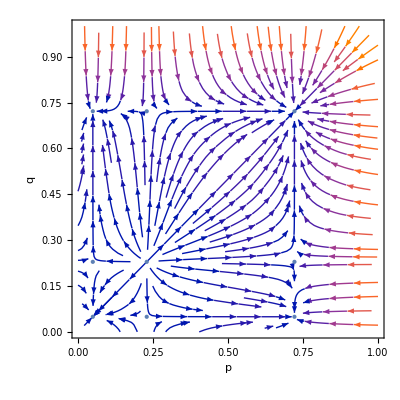

```mathematica
Show[StreamPlot[{0.0004-0.010400000000000008 p+0.049 p^2-0.049 p^3,0.0004-0.010400000000000008 q+0.049 q^2-0.049 q^3},{p,0,1},{q,0,1},FrameLabel->{Style[p,FontSize->13,FontColor->Black],Style[q,FontSize->13,FontColor->Black]}],ListPlot[NSolve[probEvolve[p,q,0,{{100,100},{0.01,0.0004,0.0005},{0.01,0.0004,0.0005},{1,0,0}}][[1;;2]]=={p,q},{p,q},PositiveReals][[All,All,2]],ColorFunctionScaling->False,ColorFunction->Function[{x,y},If[Max[eigenGrad[{x,y,0},{{100,100},{0.01,0.0004,0.0005},{0.01,0.0004,0.0005},{1,0,0}}]]>1,Red,Blue]],PlotStyle->{PointSize->Large,FontSize->14}]]
```

```mathematica
Export["/Users/anthonyjureidini/Desktop/Oxford/Michaelmas/C5.4 - Networks/Mini-Project/Flow2DnoInteraction.eps",%550,"EPS"]
```

/Users/anthonyjureidini/Desktop/Oxford/Michaelmas/C5.4 - Networks/Mini-Project/Flow2DnoInteraction.eps

```mathematica
paramOutPlot
```

{{73,73},{0.003,0.00015,0.0001515},{0.003,0.00015,0.00016},{0.00301,0.00039,6.5×10^-6}}

```mathematica
probEvolve[p,q,r,paramOutPlot]
```

{0.997 p+(1-p) (0.00015+0.0001515 (71 p^2+73 r^2)),0.997 q+(1-q) (0.00015+0.00016 (71 q^2+73 r^2)),0.99699 r+(1-r) (0.00039+6.5×10^-6 (72 p r+72 q r))}

```mathematica
Show[StreamPlot3D[probEvolve[p,q,r,paramOutPlot3D]-{p,q,r},{p,0.17,0.55},{q,0.16,0.55},{r,0.115,0.135},StreamScale->{1/10,100,0.1}],ListPointPlot3D[NSolve[probEvolve[p,q,r,paramOutPlot3D]=={p,q,r},{p,q,r},PositiveReals][[All,All,2]],ColorFunctionScaling->False,ColorFunction->Function[{x,y,z},If[Max[eigenGrad[{x,y,z},paramOutPlot3D]]>1,Red,Blue]],PlotStyle->{PointSize->Large,FontSize->14}],Axes->True,AxesLabel->{Style[p,FontSize->15,FontColor->Black],Style[q,FontSize->16,FontColor->Black],Style[r,FontSize->16,FontColor->Black]}]
```

$Aborted

```mathematica
Slice
```

```mathematica
paramOutPlot3D
```

{{73,73},{0.003,0.00015,0.0001515},{0.003,0.00015,0.0001515},{0.00301,0.00039,6.5×10^-6}}

```mathematica
NSolve[probEvolve[p,q,r,paramOutPlot]=={p,q,r},{p,q,r},PositiveReals]
```

{{p→0.521031,q→0.588069,r→0.132223}}

```mathematica
paramOutPlot
```

{{73,73},{0.003,0.00015,0.0001515},{0.003,0.00015,0.00016},{0.00301,0.00039,6.5×10^-6}}

```mathematica
NSolve[probEvolve[p,q,r,paramOutPlot3D]=={p,q,r},{p,q,r},PositiveReals][[All,All,2]]
```

{{0.519043,0.519043,0.130969},{0.260762,0.511387,0.126446},{0.511387,0.260762,0.126446},{0.216193,0.510024,0.125691},{0.510024,0.216193,0.125691},{0.296403,0.296403,0.123541},{0.188603,0.308412,0.122036},{0.308412,0.188603,0.122036},{0.178192,0.178192,0.119882}}

```mathematica
paramSymmS
```

{{n,n},{ω,δ,ϵ},{ω,δ,ϵ},{ωr,δr,ϵr}}

```mathematica
Solve[probEvolve[p,q,r,{{n,n},{ω,0,ϵ},{ω,0,ϵ},{2ω,0,ϵ/10}}]=={p,q,r},{p,q,r}]
```

$Aborted

```mathematica
Reduce[probEvolve[p,q,r,{{n,n},{ω,0,ϵ},{ω,0,ϵ},{2ω,0,ϵ/10}}]=={p,q,r},r]
```

$Aborted

```mathematica
Solve[probEvolve[p,q,r,{{n,n},{ω,0,ϵ},{ω,0,ϵ},{1/10,0,1/10}}]-{p,q,r}=={0,0,0},{p,q,r},PositiveReals,Assumptions->n∈PositiveIntegers&&0<ω<1&&0<ϵ<1&&n>1]
```

$Aborted

```mathematica
PolynomialReduce[(1-p) ((-2+n) p^2+n r^2) ϵ-p ω,{(1-q) ((-2+n) q^2+n r^2) ϵ-q ω,-1/10 (-1+n) (p+q) (-1+r) r ϵ-2 r ω},{p,q,r}]
```

{{0,-(10 n)/(1-n)},-n p r ϵ-n q r ϵ+n r^2 ϵ+n q r^2 ϵ+p^3 (2 ϵ-n ϵ)+p^2 (-2 ϵ+n ϵ)-p ω+(20 n r ω)/(-1+n)}

$Aborted

```mathematica
PolynomialRe
```

```mathematica
Manipulate[Show[Plot[(1-p)/ω*(δ+ϵ(n-2)*p^2),{p,0,1},PlotStyle->Orange],Plot[p,{p,0,1}]],{{δ,0.00015,"δ"},0,0.003,0.000005,Appearance->"Labeled"},{{ ϵ,0.0001515,"ϵ"},0.0001,0.001
,0.000001,Appearance->"Labeled"},{{ω,0.003,"ω"},0.0005,0.02,Appearance->"Labeled"},{{n,100,"n"},50,150,Appearance->"Labeled"}]
```

```mathematica
paramSym
```

{{n1,n2},{ω_p,δ_p,ϵ_p},{ω_q,δ_q,ϵ_q},{ω_r,δ_r,ϵ_r}}

```mathematica
paramTest={{100,100},{0.02,0.001,0.0008},{0.01,0.0004,0.0005},{1,0,0}}
```

{{100,100},{0.02,0.001,0.0008},{0.01,0.0004,0.0005},{1,0,0}}

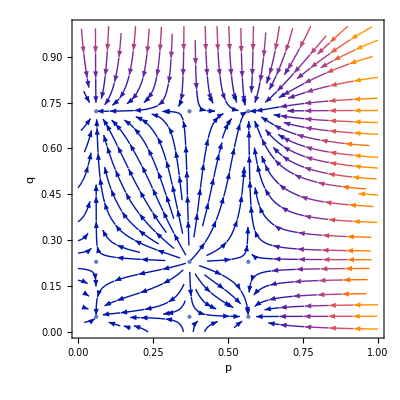

```mathematica
Show[StreamPlot[probEvolve[p,q,0,paramTest][[1;;2]]-{p,q},{p,0,1},{q,0,1},PerformanceGoal->"Quality",FrameLabel->{Style[p,FontSize->15,FontColor->Black],Style[q,FontSize->16,FontColor->Black]},VectorScaling->Automatic],ListPlot[NSolve[probEvolve[p,q,0,paramTest][[1;;2]]=={p,q},{p,q},PositiveReals][[All,All,2]],ColorFunctionScaling->False,ColorFunction->Function[{x,y},If[Max[eigenGrad[{x,y,0},paramTest]]>1,Red,Blue]],PlotStyle->{PointSize->Large,FontSize->14}]]
```

```mathematica
Project
```

```mathematica
Manipulate[paramOutPlot ={{n1,n2},{ωp,δp,ϵp},{ωq,δq,ϵq},{ωr,δr,ϵr}};With[{s=NSolve[{(1-p) (δp+((-2+n1) p^2+n2 r^2) ϵp)+p (1-ωp),(1-q) (δq+((-2+n2) q^2+n1 r^2) ϵq)+q (1-ωq),(1-r) (δr+((-1+n1) p r+(-1+n2) q r) ϵr)+r (1-ωr)}=={p,q,r},{p,q,r},PositiveReals],par = {{n1,n2},{ωp,δp,ϵp},{ωq,δq,ϵq},{ωr,δr,ϵr}}},Show[ContourPlot3D[FullSimplify[probEvolve[p,q,r,{{n1,n2},{ωp,δp,ϵp},{ωq,δq,ϵq},{ωr,δr,ϵr}}]][[1]]-p==0,{p,0,1},{q,0,1},{r,0,1},ContourStyle->{Red,Opacity[0.5]},PerformanceGoal->"Speed",PlotLegends->Style["f(p)=0",Red]],ContourPlot3D[FullSimplify[probEvolve[p,q,r,{{n1,n2},{ωp,δp,ϵp},{ωq,δq,ϵq},{ωr,δr,ϵr}}]][[2]]-q==0,{p,0,1},{q,0,1},{r,0,1},ContourStyle->{Yellow,Opacity[0.5]},PerformanceGoal->"Speed",PlotLegends->Style["g(q)=0",Blue]],ContourPlot3D[FullSimplify[probEvolve[p,q,r,{{n1,n2},{ωp,δp,ϵp},{ωq,δq,ϵq},{ωr,δr,ϵr}}]][[3]]-r==0,{p,0,1},{q,0,1},{r,0,1},ContourStyle->{Green,Opacity[0.5]},PerformanceGoal->"Speed",PlotLegends->Style["h(r)=0",Green]],ListPointPlot3D[s[[All,All,2]],ColorFunctionScaling->False,ColorFunction->Function[{x,y,z},If[Max[eigenGrad[{x,y,z},{{n1,n2},{ωp,δp,ϵp},{ωq,δq,ϵq},{ωr,δr,ϵr}}]]>1,Red,Blue]],PlotStyle->{PointSize->Large,FontSize->14}]]],{{δp,0.00015,"δ_p"},0,0.003,0.000005,Appearance->"Labeled"},{{ ϵp,0.0001515,"ϵ_p"},0,0.0006,Appearance->"Labeled"},{{ωp,0.003,"ω_p"},0.0005,0.02,Appearance->"Labeled"},{{δq,0.00015,"δ_q"},0,0.006,0.00005,Appearance->"Labeled"},{{ ϵq,0.0001515,"ϵ_q"},0.000145,0.000160,0.000001,Appearance->"Labeled"},{{ωq,0.003,"ω_q"},0.0005,0.02,Appearance->"Labeled"},{{δr,0.00039,"δ_r"},0,0.006,0.000005,Appearance->"Labeled"},{{ ϵr,6.5*10^(-6),"ϵ_r"},0,0.0006,Appearance->"Labeled"},{{ωr,0.00301,"ω_r"},0.0005,0.02,Appearance->"Labeled"},{{n1,73,"n_1"},50,200,1,Appearance->"Labeled"},{{n2,73,"n_2"},50,200,1,Appearance->"Labeled"},SaveDefinitions->True]
```

```mathematica
probEvolve[p,q,r,paramSymm][[3]]
```

(1-r) (δr+((-1+n1) p r+(-1+n2) q r) ϵr)+r (1-ωr)

```mathematica
Proje
```

```mathematica
Show[VectorPlot3D[probEvolve[p,q,r,paramSOut]-{p,q,r},{p,0.17,0.55},{q,0.16,0.55},{r,0.115,0.135},RegionFunction->Function[{p,q,r},Abs[probEvolve[p,q,r,paramSOut][[3]]-r]<0.000005],PerformanceGoal->"Quality",VectorScaling->Automatic,VectorPoints->Fine],ListPointPlot3D[NSolve[probEvolve[p,q,r,paramOutPlot3D]=={p,q,r},{p,q,r},PositiveReals][[All,All,2]],ColorFunctionScaling->False,ColorFunction->Function[{x,y,z},If[Max[eigenGrad[{x,y,z},paramSOut]]>1,Red,Blue]],PlotStyle->{PointSize->Large,FontSize->14}],Axes->True,AxesLabel->{Style[p,FontSize->15,FontColor->Black],Style[q,FontSize->16,FontColor->Black],Style[r,FontSize->16,FontColor->Black]},Boxed->False]
```

-Graphics3D-

```mathematica
VectorScaling->Automatic,VectorPoints->Fine
```

```mathematica
RegionFunction->Function[{p,q,r},probEvolve[p,q,r,paramOutPlot3D][[3]]==0]
```

```mathematica
probEvolve[x,y,z,paramOutPlot3D][[3]]
```

0.99699 z+(1-z) (0.00039+6.5×10^-6 (72 x z+72 y z))

```mathematica
Show[SliceVectorPlot3D[probEvolve[p,q,r,paramSOut]-{p,q,r},{probEvolve[p,q,r,paramSOut][[3]]-r==0},{p,0.17,0.55},{q,0.16,0.55},{r,0.115,0.135},PerformanceGoal->"Quality"],ListPointPlot3D[NSolve[probEvolve[p,q,r,paramOutPlot3D]=={p,q,r},{p,q,r},PositiveReals][[All,All,2]],ColorFunctionScaling->False,ColorFunction->Function[{x,y,z},If[Max[eigenGrad[{x,y,z},paramSOut]]>1,Red,Blue]],PlotStyle->{PointSize->0.03,FontSize->14}],Axes->True,AxesLabel->{Style[p,FontSize->15,FontColor->Black],Style[q,FontSize->16,FontColor->Black],Style[r,FontSize->16,FontColor->Black]},Boxed->False]
```

-Graphics3D-

```mathematica
paramSOut
```

{{73,73},{0.003,0.00015,0.0001515},{0.003,0.00015,0.0001515},{0.00301,0.00039,6.5×10^-6}}

```mathematica
paramSym
```

{{n1,n2},{ω_p,δ_p,ϵ_p},{ω_q,δ_q,ϵ_q},{ω_r,δ_r,ϵ_r}}

```mathematica
Manipulate[paramAvgOut ={{n,n},{ωp,δp,ϵp},{ωq,δq,ϵq},{ωp+ωq,(δp+δq)/10,(ϵp+ϵq)/10}};
With[{s=NSolve[probEvolve[p,q,r,{{n,n},{ωp,δp,ϵp},{ωq,δq,ϵq},{ωp+ωq,(δp+δq)/10,(ϵp+ϵq)/10}}]=={p,q,r},{p,q,r},PositiveReals],par = {{n,n},{ωp,δp,ϵp},{ωq,δq,ϵq},{ωp+ωq,(δp+δq)/10,(ϵp+ϵq)/10}}},Table[ToString[s[[i]]]<>", Eigenvalues: "<> ToString[eigenGrad[s[[i]][[All,2]],par]],{i,1,Length[s]}]],{{δp,0.000105,"δ_p"},0,0.001,0.000005,Appearance->"Labeled"},{{ ϵp,0.001,"ϵ_p"},0,0.003,Appearance->"Labeled"},{{ωp,0.00685,"ω_p"},0.0005,0.03,Appearance->"Labeled"},{{δq,0.00013,"δ_q"},0,0.001,0.000005,Appearance->"Labeled"},{{ ϵq,0.0002905,"ϵ_q"},0,0.0003,Appearance->"Labeled"},{{ωq,0.005,"ω_q"},0.0005,0.03,Appearance->"Labeled"},{{n,73,"n"},50,200,1,Appearance->"Labeled"},SaveDefinitions->True]
```

```mathematica
Show[SliceVectorPlot3D[probEvolve[p,q,r,paramAvgOut]-{p,q,r},{probEvolve[p,q,r,paramAvgOut][[3]]-r==0},{p,0,01},{q,0,1},{r,0,0.2},PerformanceGoal->"Quality"],ListPointPlot3D[NSolve[probEvolve[p,q,r,paramAvgOut]=={p,q,r},{p,q,r},PositiveReals][[All,All,2]],ColorFunctionScaling->False,ColorFunction->Function[{x,y,z},If[Max[eigenGrad[{x,y,z},paramAvgOut]]>1,Red,Blue]],PlotStyle->{PointSize->0.03,FontSize->14}],Axes->True,AxesLabel->{Style[p,FontSize->15,FontColor->Black],Style[q,FontSize->16,FontColor->Black],Style[r,FontSize->16,FontColor->Black]},Boxed->False]
```

-Graphics3D-

```mathematica
paramOutPlot3D
paramSym
paramSol[ϵq_] :={{73,73},{0.003,0.00015,0.0001515},{0.003,0.00015,ϵq},{0.003,0.00039,6.5*^-6}} ;
paramSoll[ϵr_] :={{73,73},{0.003,0.00015,0.0001515},{0.003,0.00015,0.0001515},{0.003,0.00039,ϵr}} ;
```

{{73,73},{0.003,0.00015,0.0001515},{0.003,0.00015,0.000145},{0.00301,0.00039,6.5×10^-6}}

{{n1,n2},{ω_p,δ_p,ϵ_p},{ω_q,δ_q,ϵ_q},{ω_r,δ_r,ϵ_r}}

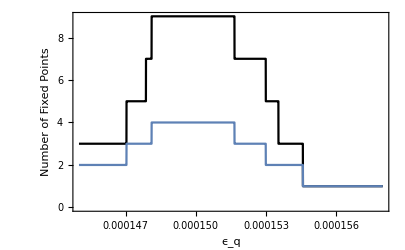

```mathematica
Show[Plot[Length[NSolve[probEvolve[p,q,r,paramSol[ϵq]]=={p,q,r},{p,q,r},PositiveReals]],{ϵq,0.000145,0.000158},PlotStyle->{Black},Frame->True,FrameLabel->{Style["ϵ_q",FontSize->14,FontColor->Black],Style["Number of Fixed Points",FontSize->14,FontColor->Black]}],Plot[countStable[NSolve[probEvolve[p,q,r,paramSol[ϵq]]=={p,q,r},{p,q,r},PositiveReals],paramSol[ϵq]],{ϵq,0.000145,0.000158}]]
```

```mathematica
Export["/Users/anthonyjureidini/Desktop/Oxford/Michaelmas/C5.4 - Networks/Mini-Project/tex/NSolParamDependency.eps",%644,"EPS"]
```

/Users/anthonyjureidini/Desktop/Oxford/Michaelmas/C5.4 - Networks/Mini-Project/tex/NSolParamDependency.eps

```mathematica
paramOut
```

{{73,73},{0.003,0.00015,0.0001515},{0.003,0.00015,0.000155},{0.00301,0.00039,6.5×10^-6}}

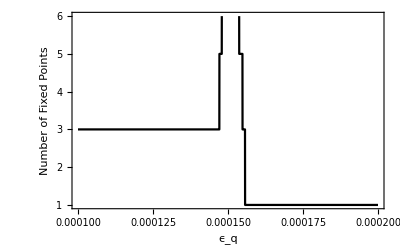

```mathematica
Plot[Length[NSolve[probEvolve[p,q,r,paramSol[ϵq]]=={p,q,r},{p,q,r},PositiveReals]],{ϵq,0.0001,0.0002},PlotStyle->{Black},Frame->True,FrameLabel->{Style["ϵ_q",FontSize->14,FontColor->Black],Style["Number of Fixed Points",FontSize->14,FontColor->Black]}]
```

```mathematica
countStable[sol__,param__]:=Module[{nSol=Length[sol]},nStable=0;For[i=1,i<=nSol,i++,If[Max[eigenGrad[sol[[i,All,2]],param]]<1,nStable=nStable+1,nStable=nStable]];nStable]
```

```mathematica
paramOutPlot3D
```

{{73,73},{0.003,0.00015,0.0001515},{0.003,0.00015,0.0001515},{0.00301,0.00039,6.5×10^-6}}

```mathematica
countStable[NSolve[probEvolve[p,q,r,paramOutPlot3D]=={p,q,r},{p,q,r},PositiveReals],paramOutPlot3D]
```

4

```mathematica
sol =NSolve[probEvolve[p,q,r,paramOutPlot3D]=={p,q,r},{p,q,r},PositiveReals]
```

{{p→0.519043,q→0.519043,r→0.130969},{p→0.260762,q→0.511387,r→0.126446},{p→0.511387,q→0.260762,r→0.126446},{p→0.216193,q→0.510024,r→0.125691},{p→0.510024,q→0.216193,r→0.125691},{p→0.296403,q→0.296403,r→0.123541},{p→0.188603,q→0.308412,r→0.122036},{p→0.308412,q→0.188603,r→0.122036},{p→0.178192,q→0.178192,r→0.119882}}

```mathematica
Max[eigenGrad[sol[[1,1]],paramOutPlot3D]]
```

eigenGrad[p→0.519043,{{73,73},{0.003,0.00015,0.0001515},{0.003,0.00015,0.0001515},{0.00301,0.00039,6.5×10^-6}}]

```mathematica
sol[[1,All,2]]
```

{0.519043,0.519043,0.130969}

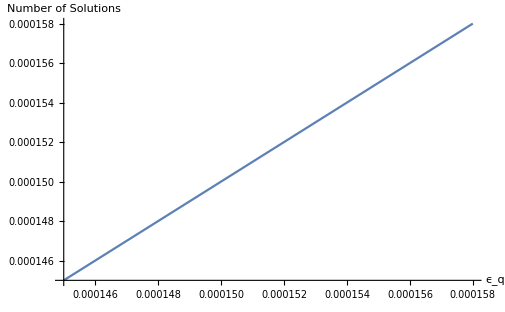

```mathematica
Plot[ϵq,{ϵq,0.000145,0.000158},Frame->True,FrameLabel->{Style["ϵ_q",FontSize->16,FontColor->Black],Style["Number of Solutions",FontSize->16,FontColor->Black]}]
```

```mathematica
paramSym
```

{{n1,n2},{ω_p,δ_p,ϵ_p},{ω_q,δ_q,ϵ_q},{ω_r,δ_r,ϵ_r}}

```mathematica
paramSymmS
```

{{n,n},{ω,δ,ϵ},{ω,δ,ϵ},{ωr,δr,ϵr}}

```mathematica
probEvolve[δp/(ωp+δp),δq/(ωq+δq),δr/(ωr+δr),paramSymm]-{δp/(ωp+δp),δq/(ωq+δq),δr/(ωr+δr)}//FullSimplify
```

{(ϵp ωp ((-2+n1) δp^2+(n2 δr^2 (δp+ωp)^2)/(δr+ωr)^2))/(δp+ωp)^3,(ϵq ωq ((-2+n2) δq^2+(n1 δr^2 (δq+ωq)^2)/(δr+ωr)^2))/(δq+ωq)^3,(δr ϵr ((-2+n1+n2) δp δq+(-1+n2) δq ωp+(-1+n1) δp ωq) ωr)/((δp+ωp) (δq+ωq) (δr+ωr)^2)}

```mathematica
probEvolve[1/2+Sqrt[1/4-ωp/ϵp/(n1+n2-2)],1/2+Sqrt[1/4-ωq/ϵq/(n1+n2-2)],1/2+Sqrt[1/4-ωr/ϵr/(n1+n2-1)],{{n1,n2},{ωp,0,ϵp},{ωq,0,ϵq},{ωr,0,ϵr}}]-{1/2+Sqrt[1/4-ωp/ϵp/(n1+n2-2)],1/2+Sqrt[1/4-ωq/ϵq/(n1+n2-2)],1/2+Sqrt[1/4-ωr/ϵr/(n1+n2-1)]}//FullSimplify
```

{1/4 (-(2 n2 ωp (1+√(1-(4 ωp)/((-2+n1+n2) ϵp))))/(-2+n1+n2)-(n2 ϵp (-1+√(1-(4 ωp)/((-2+n1+n2) ϵp))) (-2 ωr+(-1+n1+n2) ϵr (1+√(1-(4 ωr)/((-1+n1+n2) ϵr)))))/((-1+n1+n2) ϵr)),1/4 (-(2 n1 ωq (1+√(1-(4 ωq)/((-2+n1+n2) ϵq))))/(-2+n1+n2)-(n1 ϵq (-1+√(1-(4 ωq)/((-2+n1+n2) ϵq))) (-2 ωr+(-1+n1+n2) ϵr (1+√(1-(4 ωr)/((-1+n1+n2) ϵr)))))/((-1+n1+n2) ϵr)),-(ωr (1+n2 √(1-(4 ωp)/((-2+n1+n2) ϵp))-(-1+n1+n2) √(1-(4 ωp)/((-2+n1+n2) ϵp))+√(1-(4 ωq)/((-2+n1+n2) ϵq))-n2 √(1-(4 ωq)/((-2+n1+n2) ϵq))+(-1+n1+n2) √(1-(4 ωr)/((-1+n1+n2) ϵr))))/(2 (-1+n1+n2))}

```mathematica
NSolve[{p/2+(1-p)(1+p^2+r^2),q/2+(1-q)(1+q^2+r^2),r/2+(1-r)(1+r*p+r*q)}=={p,q,r},{p,q,r},PositiveReals]
```

{{p→0.825315,q→0.825315,r→0.825315}}

```mathematica
paramSymm
```

{{n1,n2},{ωp,δp,ϵp},{ωq,δq,ϵq},{ωr,δr,ϵr}}

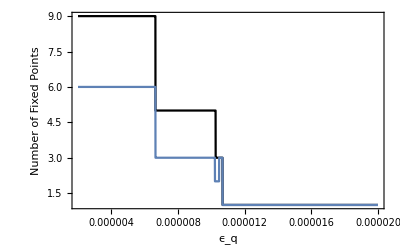

```mathematica
Show[Plot[Length[NSolve[probEvolve[p,q,r,paramSoll[ϵr]]=={p,q,r},{p,q,r},PositiveReals]],{ϵr,0.000002,0.00002},PlotStyle->{Black},Frame->True,FrameLabel->{Style["ϵ_q",FontSize->14,FontColor->Black],Style["Number of Fixed Points",FontSize->14,FontColor->Black]}],Plot[countStable[NSolve[probEvolve[p,q,r,paramSoll[ϵr]]=={p,q,r},{p,q,r},PositiveReals],paramSol[ϵr]],{ϵr,0.000002,0.00002}],PlotRange->Full]
```

```mathematica
countStable[NSolve[probEvolve[p,q,r,paramSoll[0.0000055]]=={p,q,r},{p,q,r},PositiveReals],paramSoll[0.000005]]
```

4

```mathematica
probEvolve[p,q,r,{{n,n},{ω,δ,ϵ},{ω,δ,ϵ},{1/2,10^-6,10^-4}}]
```

{p,q,r}

```mathematica
Solve[{p+(1-p) (δ+(-2+n) p^2 ϵ+n r^2 ϵ)-p ω,q+(1-q) (δ+(-2+n) q^2 ϵ+n r^2 ϵ)-q ω,r/2-((-1+r) (1+100 (-1+n) (p+q) r))/1000000}=={p,q,r},{p,q,r}]
```

$Aborted

```mathematica
probEvolve[p,q,r,{{n,n},{ω,0,ϵ},{ω,0,ϵ},{1/2,0,10^(-4)}}]//FullSimplify
```

{p+(1-p) ((-2+n) p^2+n r^2) ϵ-p ω,q+(1-q) ((-2+n) q^2+n r^2) ϵ-q ω,r/2-((-1+n) (p+q) (-1+r) r)/10000}

```mathematica
Solve[{p+(1-p) ((-2+n) p^2+n r^2) ϵ-p ω,q+(1-q) ((-2+n) q^2+n r^2) ϵ-q ω,r/2-((-1+n) (p+q) (-1+r) r)/10000}=={p,q,r},{p,q,r}]
```

$Aborted

```mathematica
probEvolve[p,q,r,paramSymm]/.ωr->1/2/.δr->10^(-6)/.ϵr->10^(-4)/.n1->n/.n2->n//FullSimplify
```

{p+(1-p) (δp+(-2+n) p^2 ϵp+n r^2 ϵp)-p ωp,q+(1-q) (δq+(-2+n) q^2 ϵq+n r^2 ϵq)-q ωq,r/2-((-1+r) (1+100 (-1+n) (p+q) r))/1000000}

```mathematica
Clear[p,q,r]
```

```mathematica
r/2-((-1+r) (1+100 (-1+n) (p+q) r))/1000000//Expand
```

1/1000000+(499999 r)/1000000-(p r)/10000+(n p r)/10000-(q r)/10000+(n q r)/10000+(p r^2)/10000-(n p r^2)/10000+(q r^2)/10000-(n q r^2)/10000

```mathematica
paramOutPlot3D
```

{{73,73},{0.0049,0.000035,0.000291},{0.003,0.0002,0.00015},{0.009,0.,0.000144}}

```mathematica
NSolve[probEvolve[p,q,r,paramOutPlot3D]=={p,q,r},{p,q,r},PositiveReals]
```

{{p→0.519043,q→0.519043,r→0.130969},{p→0.260762,q→0.511387,r→0.126446},{p→0.511387,q→0.260762,r→0.126446},{p→0.216193,q→0.510024,r→0.125691},{p→0.510024,q→0.216193,r→0.125691},{p→0.296403,q→0.296403,r→0.123541},{p→0.188603,q→0.308412,r→0.122036},{p→0.308412,q→0.188603,r→0.122036},{p→0.178192,q→0.178192,r→0.119882}}

```mathematica
dens = thDensityEvolution[NSolve[probEvolve[p,q,r,paramOutPlot3D]=={p,q,r},{p,q,r},PositiveReals][[7,All,2]],paramOutPlot3D,100000]
```

```mathematica
Show[ListPlot[dens,PlotRange->Full,PlotLabels->{1,1,1}],ListPlot[denss,PlotRange->Full]]
```

-Graphics-

```mathematica
List
```

0.617839

```mathematica
denss = thDensityEvolution[NSolve[probEvolve[p,q,r,paramOutPlot3D]=={p,q,r},{p,q,r},PositiveReals][[7,All,2]]-{0.0001,0.0001,0.0001},paramOutPlot3D,100000]
```

```mathematica
.
```

```mathematica
paramSymmS
```

{{n,n},{ω,δ,ϵ},{ω,δ,ϵ},{ωr,δr,ϵr}}

```mathematica
probEvolve[p,q,r,{{n,n},{ω,δ,ϵ},{ω,δ,ϵ},{2ω,δ/2,ϵ}}]-{p,q,r}//FullSimplify
```

{(1-p) (δ+(-2+n) p^2 ϵ+n r^2 ϵ)-p ω,(1-q) (δ+(-2+n) q^2 ϵ+n r^2 ϵ)-q ω,-1/2 (-1+r) (δ+2 (-1+n) (p+q) r ϵ)-2 r ω}

```mathematica
Manipulate[paramSimp ={{n,n},{ω,δ,ϵ},{ω,δ,ϵ},{2ω,δ/2,ϵ}};
With[{s=NSolve[probEvolve[p,q,r,{{n,n},{ω,δ,ϵ},{ω,δ,ϵ},{ω,δ/2,ϵ}}]=={p,q,r},{p,q,r},PositiveReals],par = {{n,n},{ω,δ,ϵ},{ω,δ,ϵ},{2ω,δ/2,ϵ}}},Table[ToString[s[[i]]]<>", Eigenvalues: "<> ToString[eigenGrad[s[[i]][[All,2]],par]],{i,1,Length[s]}]],{{ ϵ,0.0001,"ϵ"},0,0.01,Appearance->"Labeled"},{{ω,0.00685,"ω"},0.0005,0.05,Appearance->"Labeled"},{{δ,0.00013,"δ"},0,0.001,0.000005,Appearance->"Labeled"},{{n,73,"n"},50,200,1,Appearance->"Labeled"},SaveDefinitions->True]
```

```mathematica
0.000015/(0.0283+0.000015)
```

0.000529755

```mathematica
probEvolve[p,q,r,{{n,n},{ω,0,ϵ},{ω,0,ϵ},{2ω,0/2,ϵ}}]//FullSimplify
```

{p+(1-p) ((-2+n) p^2+n r^2) ϵ-p ω,q+(1-q) ((-2+n) q^2+n r^2) ϵ-q ω,r-(-1+n) (p+q) (-1+r) r ϵ-2 r ω}

```mathematica
Show[SliceVectorPlot3D[probEvolve[p,q,r,paramSimp]-{p,q,r},{probEvolve[p,q,r,paramSimp][[3]]-r==0},{p,0,.15},{q,0,0.15},{r,0,0.15},PerformanceGoal->"Quality",VectorScaling->Automatic],ListPointPlot3D[NSolve[probEvolve[p,q,r,paramSimp]=={p,q,r},{p,q,r},PositiveReals][[All,All,2]],ColorFunctionScaling->False,ColorFunction->Function[{x,y,z},If[Max[eigenGrad[{x,y,z},paramSimp]]>1,Red,Blue]],PlotStyle->{PointSize->0.03,FontSize->14}],Axes->True,AxesLabel->{Style[p,FontSize->15,FontColor->Black],Style[q,FontSize->16,FontColor->Black],Style[r,FontSize->16,FontColor->Black]},Boxed->False]
```

-Graphics3D-

```mathematica
probEvolve[p,q,r,paramSymmS]
```

{(1-p) (δ+((-2+n) p^2+n r^2) ϵ)+p (1-ω),(1-q) (δ+((-2+n) q^2+n r^2) ϵ)+q (1-ω),(1-r) (δr+((-1+n) p r+(-1+n) q r) ϵr)+r (1-ωr)}

```mathematica
paramSymmS
```

{{n,n},{ω,δ,ϵ},{ω,δ,ϵ},{ωr,δr,ϵr}}

```mathematica
probEvolve[p,q,r,{{n,n},{ω,δ,ϵ/(n-2)},{ω,δ,ϵ/(n-2)},{ωr,δr,ϵ/(n-1)}}]//FullSimplify
```

{p+(1-p) (δ+(p^2+(n r^2)/(-2+n)) ϵ)-p ω,q+(1-q) (δ+(q^2+(n r^2)/(-2+n)) ϵ)-q ω,δr-r (-1+δr+(p+q) (-1+r) ϵ+ωr)}

```mathematica
{p+(1-p) (δ+(p^2+ r^2) ϵ)-p ω,q+(1-q) (δ+(q^2+r^2) ϵ)-q ω,δr-r (-1+δr+(p+q) (-1+r) ϵ+ωr)}//MatrixForm
```

(p+(1-p) (δ+(p^2+r^2) ϵ)-p ω
q+(1-q) (δ+(q^2+r^2) ϵ)-q ω
δr-r (-1+δr+(p+q) (-1+r) ϵ+ωr))

```mathematica
Solve[{p+(1-p) (δ+(p^2+ r^2) ϵ)-p ω,q+(1-q) (δ+(q^2+r^2) ϵ)-q ω,δ/10-r (-1+δ/10+(p+q) (-1+r) ϵ+2ω)}=={p,q,r},{p,q,r}]
```

$Aborted

```mathematica
Reduce[probEvolve[p,q,r,{{n,n},{ω,δ,ϵ},{ω,δ,ϵ},{ω,δ/2,ϵ}}]=={p,q,r},r]
```

$Aborted

```mathematica
({p->0.754180626264681,q->0.19597520542410896,r->0.06652399112513317}[[All,2]]-{p->0.23235625017096556,q->0.2323562501709652,r->0.005951231323902256}[[All,2]])/10
```

{0.0521824,-0.0036381,0.00605728}

```mathematica
paramSym
```

{{n1,n2},{ω_p,δ_p,ϵ_p},{ω_q,δ_q,ϵ_q},{ω_r,δ_r,ϵ_r}}

```mathematica
paramOutPlot3D
```

{{73,73},{0.01924,0.000185,0.001},{0.0195,0.0003,0.0015},{0.02,0.000065,0.000278}}

```mathematica
NSolve[probEvolve[p,q,r,{{73,73},{0.02,0.0003,0.0015},{0.02,0.0003,0.0015},{0.02,0.00006,0.0003}}]=={p,q,r},{p,q,r},PositiveReals]
```

{{p→0.824497,q→0.824497,r→0.440629},{p→0.195975,q→0.754181,r→0.066524},{p→0.754181,q→0.195975,r→0.066524},{p→0.0177934,q→0.75145,r→0.0161601},{p→0.75145,q→0.0177934,r→0.0161601},{p→0.232356,q→0.232356,r→0.00595123},{p→0.0162254,q→0.232488,r→0.00407894},{p→0.232488,q→0.0162254,r→0.00407894},{p→0.0161806,q→0.0161806,r→0.00309867}}

```mathematica
s = With[{par ={{73,73},{0.02,0.0003,0.0015},{0.02,0.0003,0.0015},{0.02,0.00006,0.0003}} ,sol = NSolve[probEvolve[p,q,r,{{73,73},{0.02,0.0003,0.0015},{0.02,0.0003,0.0015},{0.02,0.00006,0.0003}}]=={p,q,r},{p,q,r},PositiveReals][[All,All,2]]},Table[eigenGrad[sol[[i]],par],{i,1,Length[sol]}]]
```

{{0.914283,0.916864,0.98675},{0.958006,0.996562,1.00998},{0.958006,0.996562,1.00998},{0.959308,0.983267,0.99612},{0.959308,0.983267,0.99612},{0.989847,1.01194,1.01195},{0.983036,0.985301,1.01195},{0.983036,0.985301,1.01195},{0.980599,0.983062,0.983098}}

```mathematica
test = densityEvolution[blockMatrix[73,73, 0.01060126805048031,0.7604747328538277,0.013433968985351362],paramOutPlot3D,1000];
```

{447.767 Out,448.966 Out,461.382 Out}

```mathematica
paramNice = {{73,73},{0.02,0.0003,0.0015},{0.02,0.0003,0.0015},{0.02,0.00006,0.0003}}
```

{{73,73},{0.02,0.0003,0.0015},{0.02,0.0003,0.0015},{0.02,0.00006,0.0003}}

{0.0106013,0.760475,0.013434}

```mathematica
Show[SliceVectorPlot3D[probEvolve[p,q,r,paramNice]-{p,q,r},{probEvolve[p,q,r,paramNice][[3]]-r==0},{p,0,01},{q,0,1},{r,0,0.7},PerformanceGoal->"Quality",VectorScaling->Automatic,VectorPoints->18,TicksStyle->13],ListPointPlot3D[NSolve[probEvolve[p,q,r,paramNice]=={p,q,r},{p,q,r},PositiveReals][[All,All,2]],ColorFunctionScaling->False,ColorFunction->Function[{x,y,z},If[Max[eigenGrad[{x,y,z},paramNice]]>1,Red,Blue]],PlotStyle->{PointSize->0.03,FontSize->18}],Axes->True,AxesLabel->{Style[p,FontSize->18,FontColor->Black],Style[q,FontSize->18,FontColor->Black],Style[r,FontSize->18
,FontColor->Black]},Boxed->False,ViewPoint->{-1.5,-1.5,0.8},ImageSize->Large]
```

-Graphics3D-

```mathematica
Export["/Users/anthonyjureidini/Desktop/Oxford/Michaelmas/C5.4 - Networks/Mini-Project/tex/3DFlow.png",%1094,"PNG",ImageResolution->1000]
```

/Users/anthonyjureidini/Desktop/Oxford/Michaelmas/C5.4 - Networks/Mini-Project/tex/3DFlow.png

```mathematica
Show[VectorPlot3D[probEvolve[p,q,r,paramNice]-{p,q,r},{p,0,0.9},{q,0,0.9},{r,0,0.5},RegionFunction->Function[{p,q,r},Abs[probEvolve[p,q,r,paramNice][[3]]-r]<0.0003],PerformanceGoal->"Quality",VectorScaling->Automatic,VectorPoints->Fine],ListPointPlot3D[NSolve[probEvolve[p,q,r,paramNice]=={p,q,r},{p,q,r},PositiveReals][[All,All,2]],ColorFunctionScaling->False,ColorFunction->Function[{x,y,z},If[Max[eigenGrad[{x,y,z},paramNice]]>1,Red,Blue]],PlotStyle->{PointSize->Large,FontSize->14}],Axes->True,AxesLabel->{Style[p,FontSize->15,FontColor->Black],Style[q,FontSize->16,FontColor->Black],Style[r,FontSize->16,FontColor->Black]},Boxed->False]
```

-Graphics3D-

-Graphics3D-

```mathematica
pqr0={p->0.23235625017096556,q->0.2323562501709652,r->0.005951231323902256}[[All,2]]
```

{0.232356,0.232356,0.00595123}

```mathematica
With[{sim = densityEvolution[blockMatrix2[paramNice[[1,1]],paramNice[[1,2]],pqr0],paramNice,100]},Show[ListPlot[sim,PlotLabels->{"(p̂)_t","(q̂)_t","(r̂)_t"},PlotStyle->PointSize[0.015],Frame->True,FrameLabel->{Style["Time Step",FontSize->16,FontColor->Black],Style["Edge Density",FontSize->16,FontColor->Black]}],ListLinePlot[TemporalData[thDensityEvolution[sim[[All,30]],paramNice,100-30],{Table[i,{i,31,100}]}],PlotStyle->{{Opacity[0.6],Thickness[0.008]},{Opacity[0.6],Thickness[0.008]},{Opacity[0.6],Thickness[0.008]}}]]]
```

-Graphics-

```mathematica
pqr = {{0.23235625017096556,0.2323562501709652,0.005951231323902256}-{0.05,0.05,0},{0.23235625017096556,0.2323562501709652,0.005951231323902256}+{0,+0.008,0},{0.23235625017096556,0.2323562501709652,0.005951231323902256}+{0.01,0.003,0.002},{0.23235625017096556,0.2323562501709652,0.005951231323902256}+{0.005,0.005,0},pqr0+{0.01,0.005,0}}
```

{{0.182356,0.182356,0.00595123},{0.232356,0.240356,0.00595123},{0.242356,0.235356,0.00795123},{0.237356,0.237356,0.00595123},{0.242356,0.237356,0.00595123}}

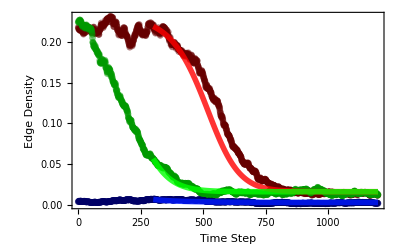

```mathematica
sim1 = With[{sim = densityEvolution[blockMatrix2[paramNice[[1,1]],paramNice[[1,2]],pqr[[1]]],paramNice,1200]},{sim,TemporalData[thDensityEvolution[sim[[All,300]],paramNice,1200-300],{Table[i,{i,301,1200}]}]}];
Show[ListPlot[sim1[[1]],(*PlotLabels->{"(p̂)_t","(q̂)_t","(r̂)_t"},*)PlotStyle->{{PointSize[0.012],Opacity[0.5],RGBColor[0.4,0,0]},{PointSize[0.012],Opacity[0.5],RGBColor[0,0.6,0]},{PointSize[0.012],Opacity[0.5],RGBColor[0,0,0.4]}},Frame->True,FrameLabel->{Style["Time Step",FontSize->15,FontColor->Black],Style["Edge Density",FontSize->15,FontColor->Black]},PlotRange->Full],ListLinePlot[sim1[[2]],PlotStyle->{{Opacity[0.8],Thickness[0.01],RGBColor[1,0,0]},{Opacity[0.8],Thickness[0.01],RGBColor[0,1,0]},{Opacity[0.8],Thickness[0.01],RGBColor[0,0.1,1]}},PlotRange->All]]
```

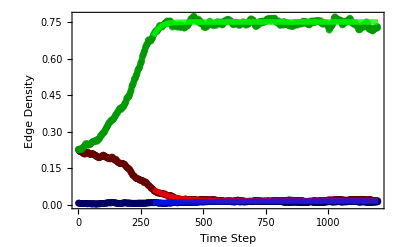

```mathematica
sim2 = With[{sim = densityEvolution[blockMatrix2[paramNice[[1,1]],paramNice[[1,2]],pqr[[1]]],paramNice,1200]},{sim,TemporalData[thDensityEvolution[sim[[All,300]],paramNice,1200-300],{Table[i,{i,301,1200}]}]}];
Show[ListPlot[sim2[[1]],(*PlotLabels->{"(p̂)_t","(q̂)_t","(r̂)_t"},*)PlotStyle->{{PointSize[0.012],Opacity[0.5],RGBColor[0.4,0,0]},{PointSize[0.012],Opacity[0.5],RGBColor[0,0.6,0]},{PointSize[0.012],Opacity[0.5],RGBColor[0,0,0.4]}},Frame->True,FrameLabel->{Style["Time Step",FontSize->15,FontColor->Black],Style["Edge Density",FontSize->15,FontColor->Black]},PlotRange->Full],ListLinePlot[sim2[[2]],PlotStyle->{{Opacity[0.8],Thickness[0.01],RGBColor[1,0,0]},{Opacity[0.8],Thickness[0.01],RGBColor[0,1,0]},{Opacity[0.8],Thickness[0.01],RGBColor[0,0.1,1]}},PlotRange->All]]
```

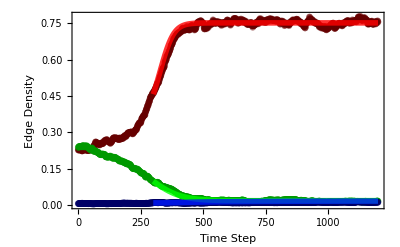

```mathematica
sim3 = With[{sim = densityEvolution[blockMatrix2[paramNice[[1,1]],paramNice[[1,2]],pqr[[1]]],paramNice,1200]},{sim,TemporalData[thDensityEvolution[sim[[All,300]],paramNice,1200-300],{Table[i,{i,301,1200}]}]}];
Show[ListPlot[sim3[[1]],(*PlotLabels->{"(p̂)_t","(q̂)_t","(r̂)_t"},*)PlotStyle->{{PointSize[0.012],Opacity[0.5],RGBColor[0.4,0,0]},{PointSize[0.012],Opacity[0.5],RGBColor[0,0.6,0]},{PointSize[0.012],Opacity[0.5],RGBColor[0,0,0.4]}},Frame->True,FrameLabel->{Style["Time Step",FontSize->15,FontColor->Black],Style["Edge Density",FontSize->15,FontColor->Black]},PlotRange->Full],ListLinePlot[sim3[[2]],PlotStyle->{{Opacity[0.8],Thickness[0.01],RGBColor[1,0,0]},{Opacity[0.8],Thickness[0.01],RGBColor[0,1,0]},{Opacity[0.8],Thickness[0.01],RGBColor[0,0.1,1]}},PlotRange->All]]
```

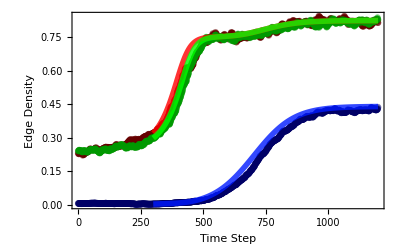

```mathematica
sim4 = With[{sim = densityEvolution[blockMatrix2[paramNice[[1,1]],paramNice[[1,2]],pqr0],paramNice,1200]},{sim,TemporalData[thDensityEvolution[sim[[All,300]],paramNice,1200-300],{Table[i,{i,301,1200}]}]}];
Show[ListPlot[sim4[[1]],(*PlotLabels->{"(p̂)_t","(q̂)_t","(r̂)_t"},*)PlotStyle->{{PointSize[0.012],Opacity[0.5],RGBColor[0.4,0,0]},{PointSize[0.012],Opacity[0.5],RGBColor[0,0.6,0]},{PointSize[0.012],Opacity[0.5],RGBColor[0,0,0.4]}},Frame->True,FrameLabel->{Style["Time Step",FontSize->15,FontColor->Black],Style["Edge Density",FontSize->15,FontColor->Black]},PlotRange->Full],ListLinePlot[sim4[[2]],PlotStyle->{{Opacity[0.8],Thickness[0.01],RGBColor[1,0,0]},{Opacity[0.8],Thickness[0.01],RGBColor[0,1,0]},{Opacity[0.8],Thickness[0.01],RGBColor[0,0.1,1]}},PlotRange->All]]
```

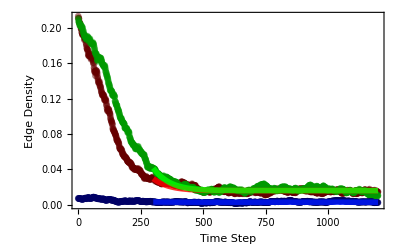

```mathematica
sim5 = With[{sim = densityEvolution[blockMatrix2[paramNice[[1,1]],paramNice[[1,2]],pqr[[1]]],paramNice,1200]},{sim,TemporalData[thDensityEvolution[sim[[All,300]],paramNice,1200-300],{Table[i,{i,301,1200}]}]}];
Show[ListPlot[sim5[[1]],(*PlotLabels->{"(p̂)_t","(q̂)_t","(r̂)_t"},*)PlotStyle->{{PointSize[0.012],Opacity[0.5],RGBColor[0.4,0,0]},{PointSize[0.012],Opacity[0.5],RGBColor[0,0.6,0]},{PointSize[0.012],Opacity[0.5],RGBColor[0,0,0.4]}},Frame->True,FrameLabel->{Style["Time Step",FontSize->15,FontColor->Black],Style["Edge Density",FontSize->15,FontColor->Black]},PlotRange->Full],ListLinePlot[sim5[[2]],PlotStyle->{{Opacity[0.8],Thickness[0.01],RGBColor[1,0,0]},{Opacity[0.8],Thickness[0.01],RGBColor[0,1,0]},{Opacity[0.8],Thickness[0.01],RGBColor[0,0.1,1]}},PlotRange->All]]
```

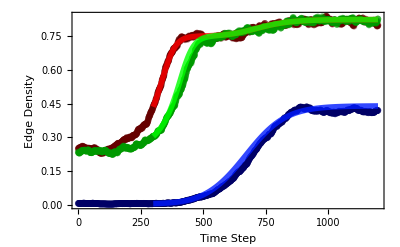

```mathematica
sim6 = With[{sim = densityEvolution[blockMatrix2[paramNice[[1,1]],paramNice[[1,2]],pqr[[3]]],paramNice,1200]},{sim,TemporalData[thDensityEvolution[sim[[All,300]],paramNice,1200-300],{Table[i,{i,301,1200}]}]}];
Show[ListPlot[sim6[[1]],(*PlotLabels->{"(p̂)_t","(q̂)_t","(r̂)_t"},*)PlotStyle->{{PointSize[0.012],Opacity[0.5],RGBColor[0.4,0,0]},{PointSize[0.012],Opacity[0.5],RGBColor[0,0.6,0]},{PointSize[0.012],Opacity[0.5],RGBColor[0,0,0.4]}},Frame->True,FrameLabel->{Style["Time Step",FontSize->15,FontColor->Black],Style["Edge Density",FontSize->15,FontColor->Black]},PlotRange->Full],ListLinePlot[sim6[[2]],PlotStyle->{{Opacity[0.8],Thickness[0.01],RGBColor[1,0,0]},{Opacity[0.8],Thickness[0.01],RGBColor[0,1,0]},{Opacity[0.8],Thickness[0.01],RGBColor[0,0.1,1]}},PlotRange->All]]
```

```mathematica
GraphicsGrid[Partition[Table[With[{sim = densityEvolution[blockMatrix2[paramNice[[1,1]],paramNice[[1,2]],pqr[[i]]],paramNice,1200]},Show[ListPlot[sim,(*PlotLabels->{"(p̂)_t","(q̂)_t","(r̂)_t"},*)PlotStyle->{{PointSize[0.012],Opacity[0.5],RGBColor[0.4,0,0]},{PointSize[0.012],Opacity[0.5],RGBColor[0,0.6,0]},{PointSize[0.012],Opacity[0.5],RGBColor[0,0,0.4]}},Frame->True,FrameLabel->{Style["Time Step",FontSize->18,FontColor->Black],Style["Edge Density",FontSize->18,FontColor->Black]},PlotRange->Full,FrameTicksStyle->Directive[FontSize->14]],ListLinePlot[TemporalData[thDensityEvolution[sim[[All,300]],paramNice,1200-300],{Table[i,{i,301,1200}]}],PlotStyle->{{Opacity[0.8],Thickness[0.01],RGBColor[1,0,0]},{Opacity[0.8],Thickness[0.01],RGBColor[0,1,0]},{Opacity[0.8],Thickness[0.01],RGBColor[0,0.1,1]}},PlotRange->All]]],{i,1,4}],2],Spacings->{0,0},ImageSize->Full]
```

$Aborted

```mathematica
Export["/Users/anthonyjureidini/Desktop/Oxford/Michaelmas/C5.4 - Networks/Mini-Project/tex/multiStability.pdf",%1329,"PDF",ImageResolution->3000]
```

/Users/anthonyjureidini/Desktop/Oxford/Michaelmas/C5.4 - Networks/Mini-Project/tex/multiStability.pdf

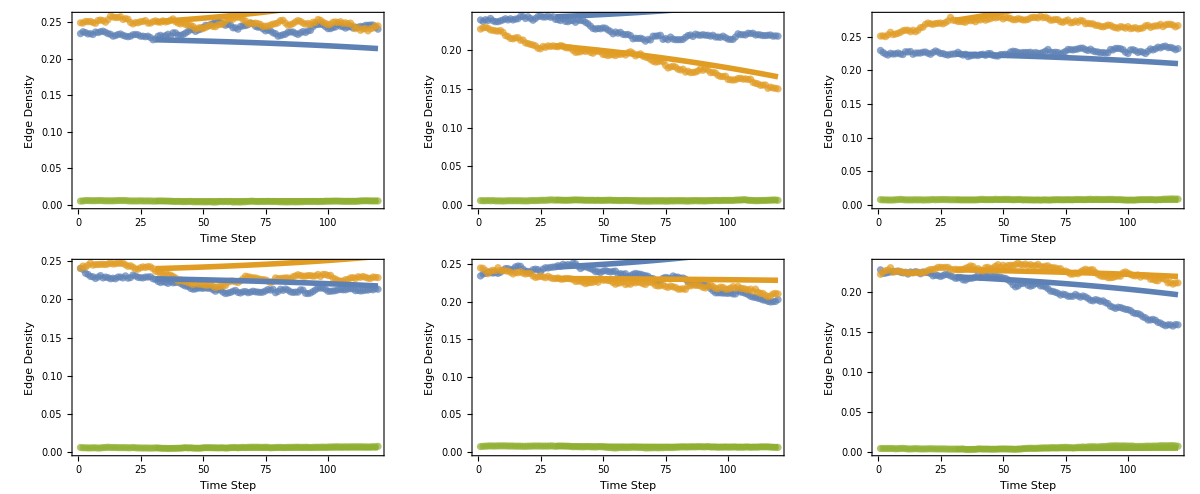

```mathematica
GraphicsGrid[Partition[Table[With[{sim = densityEvolution[blockMatrix2[paramNice[[1,1]],paramNice[[1,2]],pqr0],paramNice,120]},Show[ListPlot[sim,(*PlotLabels->{"(p̂)_t","(q̂)_t","(r̂)_t"},*)PlotStyle->{{PointSize[0.013],Opacity[0.7]},{PointSize[0.013],Opacity[0.7]},{PointSize[0.013],Opacity[0.7]}},Frame->True,FrameLabel->{Style["Time Step",FontSize->18,FontColor->Black],Style["Edge Density",FontSize->18,FontColor->Black]},FrameTicksStyle->Directive[FontSize->14]],ListLinePlot[TemporalData[thDensityEvolution[sim[[All,30]],paramNice,120-30],{Table[i,{i,31,120}]}],PlotStyle->{{Opacity[1],Thickness[0.01]},{Opacity[1],Thickness[0.01]},{Opacity[01],Thickness[0.01]}}]]],{i,1,6}],3],Spacings->{0,0},ImageSize->Full]
```

```mathematica
simulations={sim5,sim2,sim7,sim4,sim3,sim1};
GraphicsGrid[Partition[Table[Show[
ListPlot[simulations[[i]][[1]],(*PlotLabels->{"(p̂)_t","(q̂)_t","(r̂)_t"},*)PlotStyle->{{PointSize[0.012],Opacity[0.5],RGBColor[1,0,0]},{PointSize[0.012],Opacity[0.5],RGBColor[0.2,01,0.2]},{PointSize[0.012],Opacity[0.7],RGBColor[0,0.3,1]}},Frame->True,FrameLabel->{Style["Time",FontSize->14,FontColor->Black],Style["Edge Density",FontSize->14,FontColor->Black]},PlotRange->Full,FrameTicksStyle->Directive[FontSize->10]],ListLinePlot[simulations[[i]][[2]],PlotStyle->{{Opacity[1],Thickness[0.012],RGBColor[0.5,0,0]},{Opacity[1],Thickness[0.012],RGBColor[0,0.5,0]},{Opacity[1],Thickness[0.012],RGBColor[0,0,0.5]}},PlotRange->All]
],{i,1,6}
],3
],Spacings->{10,0},ImageSize->{1000,400}
]
```

-Graphics-

```mathematica
sim7 = With[{sim = densityEvolution[blockMatrix2[paramNice[[1,1]],paramNice[[1,2]],pqr[[3]]],paramNice,1200]},{sim,TemporalData[thDensityEvolution[sim[[All,300]],paramNice,1200-300],{Table[i,{i,301,1200}]}]}];
Show[ListPlot[sim7[[1]],(*PlotLabels->{"(p̂)_t","(q̂)_t","(r̂)_t"},*)PlotStyle->{{PointSize[0.012],Opacity[0.5],RGBColor[0.4,0,0]},{PointSize[0.012],Opacity[0.5],RGBColor[0,0.6,0]},{PointSize[0.012],Opacity[0.5],RGBColor[0,0,0.4]}},Frame->True,FrameLabel->{Style["Time Step",FontSize->15,FontColor->Black],Style["Edge Density",FontSize->15,FontColor->Black]},PlotRange->Full],ListLinePlot[sim7[[2]],PlotStyle->{{Opacity[0.8],Thickness[0.01],RGBColor[1,0,0]},{Opacity[0.8],Thickness[0.01],RGBColor[0,1,0]},{Opacity[0.8],Thickness[0.01],RGBColor[0,0.1,1]}},PlotRange->All]]
```

-Graphics-

```mathematica
Manipulate[paramOutFlow ={{n1,n2},{ωp,δp,ϵp},{ωq,δq,ϵq},{ωr,δr,ϵr}};With[{s=NSolve[{(1-p) (δp+((-2+n1) p^2+n2 r^2) ϵp)+p (1-ωp),(1-q) (δq+((-2+n2) q^2+n1 r^2) ϵq)+q (1-ωq),(1-r) (δr+((-1+n1) p r+(-1+n2) q r) ϵr)+r (1-ωr)}=={p,q,r},{p,q,r},PositiveReals][[All,All,2]],par = {{n1,n2},{ωp,δp,ϵp},{ωq,δq,ϵq},{ωr,δr,ϵr}}},Show[SliceVectorPlot3D[probEvolve[p,q,r,{{n1,n2},{ωp,δp,ϵp},{ωq,δq,ϵq},{ωr,δr,ϵr}}]-{p,q,r},{probEvolve[p,q,r,{{n1,n2},{ωp,δp,ϵp},{ωq,δq,ϵq},{ωr,δr,ϵr}}][[3]]-r==0},{p,Min[s[[All,1]]]-0.05,Max[s[[All,1]]+0.05]},{q,Min[s[[All,2]]]-0.05,Max[s[[All,2]]+0.05]},{r,Min[s[[All,3]]]-0.05,Max[s[[All,3]]+0.05]},PerformanceGoal->"Speed",VectorPoints->10,TicksStyle->13],ListPointPlot3D[s,ColorFunctionScaling->False,ColorFunction->Function[{x,y,z},If[Max[eigenGrad[{x,y,z},{{n1,n2},{ωp,δp,ϵp},{ωq,δq,ϵq},{ωr,δr,ϵr}}]]>1,Red,Blue]],PlotStyle->{PointSize->0.03,FontSize->18}],Axes->True,AxesLabel->{Style[p,FontSize->18,FontColor->Black],Style[q,FontSize->18,FontColor->Black],Style[r,FontSize->18
,FontColor->Black]},Boxed->False,ViewPoint->{-1.5,-1.5,0.8},ImageSize->Large]],{{δp,0.00015,"δ_p"},0,0.003,0.000005,Appearance->"Labeled"},{{ ϵp,0.0001515,"ϵ_p"},0,0.0006,Appearance->"Labeled"},{{ωp,0.003,"ω_p"},0.0005,0.02,Appearance->"Labeled"},{{δq,0.00015,"δ_q"},0,0.006,0.00005,Appearance->"Labeled"},{{ ϵq,0.0001515,"ϵ_q"},0.000145,0.000160,0.000001,Appearance->"Labeled"},{{ωq,0.003,"ω_q"},0.0005,0.02,Appearance->"Labeled"},{{δr,0.00039,"δ_r"},0,0.006,0.000005,Appearance->"Labeled"},{{ ϵr,6.5*10^(-6),"ϵ_r"},0,0.0006,Appearance->"Labeled"},{{ωr,0.00301,"ω_r"},0.0005,0.02,Appearance->"Labeled"},{{n1,73,"n_1"},50,200,1,Appearance->"Labeled"},{{n2,73,"n_2"},50,200,1,Appearance->"Labeled"},SaveDefinitions->True]
```

```mathematica
NSolve[probEvolve[p,q,r,paramNice]=={p,q,r},{p,q,r},Reals]
```

{{p→0.75129,q→0.75129,r→-0.00478053},{p→0.824497,q→0.824497,r→0.440629},{p→0.224024,q→0.752061,r→-0.034337},{p→0.752061,q→0.224024,r→-0.034337},{p→0.123414,q→0.756541,r→-0.090341},{p→0.756541,q→0.123414,r→-0.090341},{p→0.195975,q→0.754181,r→0.066524},{p→0.754181,q→0.195975,r→0.066524},{p→0.0177934,q→0.75145,r→0.0161601},{p→0.75145,q→0.0177934,r→0.0161601},{p→0.232356,q→0.232356,r→0.00595123},{p→0.0162254,q→0.232488,r→0.00407894},{p→0.232488,q→0.0162254,r→0.00407894},{p→0.0161806,q→0.0161806,r→0.00309867}}

```mathematica
Manipulate[paramOutPlot3D ={{n1,n2},{ωp,δp,ϵp},{ωq,δq,ϵq},{ωr,δr,ϵr}};With[{s=NSolve[{(1-p) (δp+((-2+n1) p^2+n2 r^2) ϵp)+p (1-ωp),(1-q) (δq+((-2+n2) q^2+n1 r^2) ϵq)+q (1-ωq),(1-r) (δr+((-1+n1) p r+(-1+n2) q r) ϵr)+r (1-ωr)}=={p,q,r},{p,q,r},NonNegativeReals],par = {{n1,n2},{ωp,δp,ϵp},{ωq,δq,ϵq},{ωr,δr,ϵr}}},Show[ListPointPlot3D[s[[All,All,2]],AxesLabel->{p,q,r},ColorFunctionScaling->False,ColorFunction->Function[{x,y,z},If[10*Max[eigenGrad[{x,y,z},{{n1,n2},{ωp,δp,ϵp},{ωq,δq,ϵq},{ωr,δr,ϵr}}]]>10,Red,Blue]]]]],{{δp,0.0004,"δ_p"},0,0.003,0.000005,Appearance->"Labeled"},{{ ϵp,0.0005,"ϵ_p"},0,0.001,Appearance->"Labeled"},{{ωp,0.01,"ω_p"},0.0005,0.03,Appearance->"Labeled"},{{δq,0.0004,"δ_q"},0,0.003,0.00005,Appearance->"Labeled"},{{ ϵq,0.0005,"ϵ_q"},0,0.001,0.00001,Appearance->"Labeled"},{{ωq,0.01,"ω_q"},0.0005,0.02,Appearance->"Labeled"},{{δr,0,"δ_r"},0,0.0005,0.000005,Appearance->"Labeled"},{{ ϵr,0,"ϵ_r"},0,0.002,Appearance->"Labeled"},{{ωr,1,"ω_r"},0,1,0.001,Appearance->"Labeled"},{{n1,100,"n_1"},50,200,1,Appearance->"Labeled"},{{n2,100,"n_2"},50,200,1,Appearance->"Labeled"},SaveDefinitions->True]
```

```mathematica
NSolve[probEvolve[p,q,r,paramOutPlot3D]=={p,q,r},{p,q,r},NonNegativeReals]
```

{{p→0.684121,q→0.69236,r→0.137902},{p→0.335703,q→0.67496,r→0.0255523},{p→0.651444,q→0.290211,r→0.0153609},{p→0.00870731,q→0.674384,r→0.0109152},{p→0.651076,q→0.0344865,r→0.0084524},{p→0.340482,q→0.291168,r→0.00858748},{p→0.340806,q→0.0343083,r→0.005855},{p→0.00819754,q→0.291404,r→0.00579499},{p→0.00811289,q→0.0342368,r→0.00439823}}

```mathematica
NonNeg
```

```mathematica
NSolve[probEvolve[p,q,r,paramNice]=={p,q,r},{p,q,r},PositiveReals]
```

{{p→0.824497,q→0.824497,r→0.440629},{p→0.195975,q→0.754181,r→0.066524},{p→0.754181,q→0.195975,r→0.066524},{p→0.0177934,q→0.75145,r→0.0161601},{p→0.75145,q→0.0177934,r→0.0161601},{p→0.232356,q→0.232356,r→0.00595123},{p→0.0162254,q→0.232488,r→0.00407894},{p→0.232488,q→0.0162254,r→0.00407894},{p→0.0161806,q→0.0161806,r→0.00309867}}

```mathematica
NSolve[probEvolve[p,q,r,paramNice]=={p,q,r},{p,q,r},Reals]
```

{{p→0.75129,q→0.75129,r→-0.00478053},{p→0.824497,q→0.824497,r→0.440629},{p→0.224024,q→0.752061,r→-0.034337},{p→0.752061,q→0.224024,r→-0.034337},{p→0.123414,q→0.756541,r→-0.090341},{p→0.756541,q→0.123414,r→-0.090341},{p→0.195975,q→0.754181,r→0.066524},{p→0.754181,q→0.195975,r→0.066524},{p→0.0177934,q→0.75145,r→0.0161601},{p→0.75145,q→0.0177934,r→0.0161601},{p→0.232356,q→0.232356,r→0.00595123},{p→0.0162254,q→0.232488,r→0.00407894},{p→0.232488,q→0.0162254,r→0.00407894},{p→0.0161806,q→0.0161806,r→0.00309867}}

```mathematica
Manipulate[Plot[probEvolve[p,q,r,paramNice][[1]],{p,0,1}],{q,0,1},{r,0,1}]
```

Part::partd: Part specification paramNice⟦1,1⟧ is longer than depth of object.

Part::partd: Part specification paramNice⟦1,2⟧ is longer than depth of object.

Part::partd: Part specification paramNice⟦2,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.